```mathematica
Clear["Global`*"]
```

```mathematica
Off[General::spell];
Off[General::spell1];
```

```mathematica
U[x_]:=If[x<-a || x>a,0,V]
```

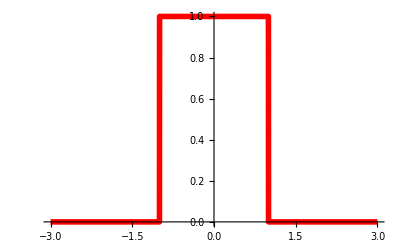

```mathematica
Plot[U[x]/.a->1/.V->1,{x,-3,3}, PlotStyle->{{Hue[1.0],Thickness[0.01]}}, PlotRange->All]
```

```mathematica
ψinc[x_]=ⅇ^(ⅈ k x);
ψrefl[x_]=R ⅇ^(-ⅈ k x);
ψwell[x_]=A ⅇ^(q x)+B ⅇ^(-q x);
ψtran[x_]=T ⅇ^(ⅈ k x);
```

```mathematica
ks={k->√(2 m En)/ℏ,q->√(2 m (V-En))/ℏ};
```

```mathematica
bc={(ψinc[x]+ψrefl[x]-ψwell[x]/.x->-a)==0,(ψwell[x]-ψtran[x]/.x->a)==0,(D[ψinc[x]+ψrefl[x],x]-D[ψwell[x] ,x]/.x->-a)==0,
(D[ψwell[x],x]-D[ψtran[x],x]/.x->a)==0} //Simplify
```

{A ⅇ^(-a q)+B ⅇ^(a q)==ⅇ^(-ⅈ a k)+ⅇ^(ⅈ a k) R,B ⅇ^(-a q)+A ⅇ^(a q)==ⅇ^(ⅈ a k) T,ⅈ ⅇ^(-ⅈ a k) k+B ⅇ^(a q) q-ⅈ ⅇ^(ⅈ a k) k R==A ⅇ^(-a q) q,A ⅇ^(a q) q-ⅈ ⅇ^(ⅈ a k) k T==B ⅇ^(-a q) q}

```mathematica
ABRandT=Solve[bc,{A,B,R,T}][[1]] //FullSimplify
```

{A→-(2 ⅇ^(a (-ⅈ k+q)) k (k-ⅈ q))/(-(k-ⅈ q)^2+ⅇ^(4 a q) (k+ⅈ q)^2),B→(2 ⅇ^(-ⅈ a k+3 a q) k (k+ⅈ q))/(-(k-ⅈ q)^2+ⅇ^(4 a q) (k+ⅈ q)^2),R→(ⅇ^(-2 ⅈ a k) (-1+ⅇ^(4 a q)) (k^2+q^2))/(-(k-ⅈ q)^2+ⅇ^(4 a q) (k+ⅈ q)^2),T→(4 ⅈ ⅇ^(2 a (-ⅈ k+q)) k q)/(-(k-ⅈ q)^2+ⅇ^(4 a q) (k+ⅈ q)^2)}

```mathematica
values={m->1,ℏ->1};
```

```mathematica
plotψ[wave_,V0_,E0_,a0_,thickness_,col_,xrange_]:=Plot[Re[ wave/.ABRandT/.ks/.values/.V->V0/.En->E0/.a->a0 ],xrange,PlotStyle->{Hue[col],Thickness[thickness]},PlotRange->{{-12,12} ,{-3,3}},AxesStyle->Transparent]
```

```mathematica
wave2D[ V0_,E0_,a0_,xmin_,xmax_]:=Show[{plotψ[(ψinc[x]+ψrefl[x]),V0,E0,a0,0.004,0.3,{x,xmin,-a0}],plotψ[ψwell[x],V0,E0,a0,0.004,0.6,{x,-a0,a0}],plotψ[ψtran[x],V0,E0,a0,0.004,0.9,{x,a0,xmax}],Graphics[{Thickness[.003],RGBColor[1,0,0],{
Line[{{xmin,-2},{-a0,-2}}],
Line[{{-a0,-2},{-a0,2}}],
Line[{{-a0,2},{a0,2}}],
Line[{{a0,2},{a0,-2}}],
Line[{{a0,-2},{xmax,-2}}]}}]}]
```

```mathematica
Manipulate[wave2D[V0,E0,a0,-12,12],{{V0,1.5,"Barrier Potential"},1,5,0.1,Appearance->"Labeled"},{{E0,1,"Particle Energy"},0.01,5,0.01,Appearance->"Labeled"},{{a0,2,"Half Barrier Width" },2,5,0.05,Appearance->"Labeled"}]
```